```mathematica
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
```

```mathematica
getTransMat[n_] := Table[PDF[BinomialDistribution[2 n, i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen]]][j],{i,0,2n},{j,0,2n}]
```

```mathematica
getTransMat[1]/.α->0 //MatrixForm
```

(1 | 0 | 0
1/4 | 1/2 | 1/4
0 | 0 | 1)

```mathematica
Table[getTransMat[1]/.gen->i-1,{i,2}]
```

{{{1,0,0},{(1/2-(α Λ)/(4 w))^2,2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)),(1/2+(α Λ)/(4 w))^2},{0,0,1}},{{1,0,0},{(1/2-(ⅇ^(-vg/w) α Λ)/(4 w))^2,2 (1/2-(ⅇ^(-vg/w) α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w)),(1/2+(ⅇ^(-vg/w) α Λ)/(4 w))^2},{0,0,1}}}

```mathematica
%[[1]] //MatrixForm
```

(1 | 0 | 0
(1/2-(α Λ)/(4 w))^2 | 2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) | (1/2+(α Λ)/(4 w))^2
0 | 0 | 1)

```mathematica
%%[[2]] //MatrixForm
```

(1 | 0 | 0
(1/2-(ⅇ^(-vg/w) α Λ)/(4 w))^2 | 2 (1/2-(ⅇ^(-vg/w) α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w)) | (1/2+(ⅇ^(-vg/w) α Λ)/(4 w))^2
0 | 0 | 1)

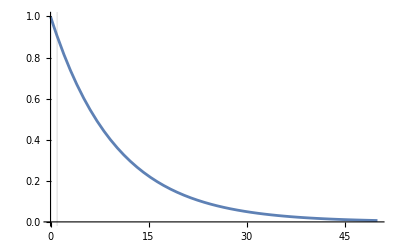

```mathematica
Plot[Exp[-0.1 gen],{gen,0,50},
GridLines->{{1},{}}]
```

```mathematica
Dot @@ Table[getTransMat[1]/.gen->i-1,{i,2}]//MatrixForm
```

(1 | 0 | 0
(1/2-(α Λ)/(4 w))^2+2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2-(ⅇ^(-vg/w) α Λ)/(4 w))^2 | 4 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2-(ⅇ^(-vg/w) α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w)) | (1/2+(α Λ)/(4 w))^2+2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w))^2
0 | 0 | 1)

```mathematica
{0,1,0}. %
```

{(1/2-(α Λ)/(4 w))^2+2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2-(ⅇ^(-vg/w) α Λ)/(4 w))^2,4 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2-(ⅇ^(-vg/w) α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w)),(1/2+(α Λ)/(4 w))^2+2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w))^2}

```mathematica
Dimensions[%]
```

{3}

```mathematica
Dimensions[%10]
```

{3,3}

```mathematica
{{0,1,0}}.%10
```

{{(1/2-(α Λ)/(4 w))^2+2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2-(ⅇ^(-vg/w) α Λ)/(4 w))^2,4 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2-(ⅇ^(-vg/w) α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w)),(1/2+(α Λ)/(4 w))^2+2 (1/2-(α Λ)/(4 w)) (1/2+(α Λ)/(4 w)) (1/2+(ⅇ^(-vg/w) α Λ)/(4 w))^2}}

```mathematica
Dimensions[%]
```

{1,3}

```mathematica
{{0,1,0}} //Dimensions
```

{1,3}

```mathematica
%14 /.{α->0.01, Λ->1,w->1, vg->0.01}
```

{{0.371269,0.249988,0.378744}}

```mathematica
Flatten[%]//Total
```

1.

```mathematica
%14/.{α->0}
```

{{3/8,1/4,3/8}}

```mathematica
3/8//N
```

0.375

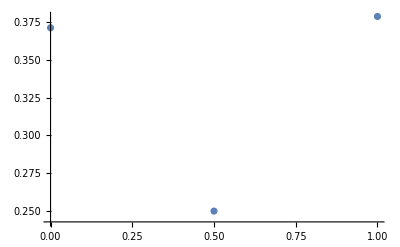

```mathematica
ListPlot[%14 /.{α->0.01, Λ->1,w->1, vg->0.01}, DataRange->{0,1}]
```